```mathematica
d1=40; h1=30; dpillar=5;hpillar=20; 
valvePlate=Line[{{0,0},{d1,0}}]
centerLine=Line[{{d1/2,0},{d1/2,h1}}]
pillarLeft=Line[{{d1/2-dpillar/2,0},{d1/2-dpillar/2,hpillar}}]
pillarLeftRight=Line[{{d1/2+dpillar/2,0},{d1/2+dpillar/2,hpillar}}]
pillar={pillarLeft,pillarLeftRight};
valve={valvePlate,centerLine,pillar}
```

Line[{{0,0},{40,0}}]

Line[{{20,0},{20,30}}]

Line[{{35/2,0},{35/2,20}}]

Line[{{45/2,0},{45/2,20}}]

{Line[{{0,0},{40,0}}],Line[{{20,0},{20,30}}],{Line[{{35/2,0},{35/2,20}}],Line[{{45/2,0},{45/2,20}}]}}

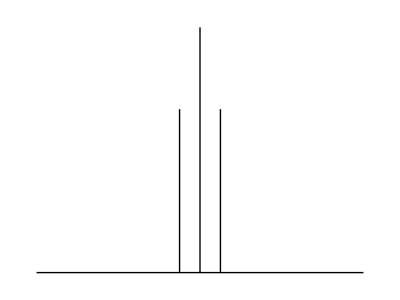

```mathematica
Graphics[valve]
```